## Useful functions

```mathematica
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->12,Magnification->1.6};
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/kirscher/kette_repo/31_resonances/code

```mathematica
RiccatiBesselJ[z_,l_]:=z SphericalBesselJ[l,z];
RiccatiBesselN[z_,l_]:=(-1.)^l z SphericalBesselY[l,z];
```

```mathematica
(*Boundery conditions for the wavefunction*)
alpha[ra_,ka_,la_,ha_]:=RiccatiBesselN[ka (ra+ha),la]/RiccatiBesselN[ka ra,la]

beta[rb_,kb_,lb_,hb_]:=RiccatiBesselJ[kb (rb+hb),lb]-RiccatiBesselJ[kb rb,lb] (RiccatiBesselN[kb (rb+hb),lb]/RiccatiBesselN[kb rb,lb])
```

LEC=(Λ,a_(3-1)^(S-wave) [fm],C_(2-body) [MeV],C_(3-body) [MeV])
the triton-proton S-wave scattering length is used to calibrate the core parameter and
was obtained by R. Lazauskas.

```mathematica
(* Nuclear E2=2.22 E3=8.48 ℏc=198*)
(* λ a0,r0 (Martin, 23) a1,r1 (Martin,45) a0 (Rimas, unprojected, 6) a1 (Rimas, unprojected, 7) a0 (Rimas, projected, 8) a1 (Rimas, projected, 9)*)
a0a1NUCLmartinrimas=Import[NotebookDirectory[]<>"../data/a0-a1_nucl_Rimas-Martin.dat","Table"][[2;;]];
(* λ C0,D0 (Martin, 23) C0,D0 (Rimas, unprojected, 45) C0,Do (Rimas, projected, 67)*)
LECsNUCLmartinrimas=Import[NotebookDirectory[]<>"../data/LECs_nucl_Rimas-Martin.dat","Table"][[2;;]];
LECsUNITmartinrimas=Import[NotebookDirectory[]<>"../data/LECs_univ_Rimas-Martin.dat","Table"][[2;;]];

activeLEC=LECsNUCLmartinrimas[[All,{1,2,3}]];
```

(non)local resonating-group potentials from a 2- and 3-body contact interaction for TRIMER-FERMION (ABC-A)

W_(non-local) takes the Energy (e_) in [MeV]

```mathematica
NormTF[core_?ArrayQ]:=1./Sqrt[Total[Flatten[Table[core[[i]][[1]] core[[j]][[1]] (Pi/(core[[i]][[2]]+core[[j]][[2]]))^1.5,{i,Length[core]},{j,Length[core]}]]]];

VlocTF[r_,lam_,Cc_,Dd_,Aa_,Bb_]:=Block[{eta2,eta3,w2,w3},
eta2=2. Cc/(2. (Aa+Bb)(3. Aa+3. Bb+2. lam))^(3./2.);
w2=3. (Aa+Bb) lam/(3. (Aa+Bb)+2. lam);
eta3=Dd/(6. (Aa+Bb)^2+16. (Aa+Bb) lam+2. lam^2)^(3./2.);
w3=(3. (Aa+Bb) lam ((Aa+Bb)+2. lam)/(3. (Aa+Bb)^2+8. (Aa+Bb) lam+lam^2));
eta2 Exp[-w2 r^2]+eta3  Exp[-w3 r^2]
];

WnolocTF[r_,rp_,Ee_,lam_,Cc_,Dd_,Aa_,Bb_,Ll_,TwoMyOverHBsq_]:=Block[{zeta1,zeta2,zeta3,a1,b1,c1,a2,b2,c2,a3,b3,c3},
zeta1=(27./64.)(2 (Aa+Bb))^(-3./2.) (1./TwoMyOverHBsq);
a1=(Aa+9. Bb) 3./32.;
b1=(Aa+Bb) 9./16.;
c1=(9. Aa+Bb) 3./32.;

zeta2=-27./32. Cc/(2. (Aa+Bb)+lam)^(3./2.);
zeta3=-27./64. Dd/(2  (Aa+Bb)+5 lam)^(3./2.);

a2=3. (Aa^2+9. Bb^2+10. Aa Bb+(14. Aa+18. Bb) lam)/(16. (2. (Aa+Bb)+lam));
b2=18. (Aa+Bb) ((Aa+Bb)+2. lam)/(16. (2. (Aa+Bb)+lam));
c2=3. (9. Aa^2+Bb^2+10. Aa Bb+(6. Aa+2. Bb) lam)/(16. (2. (Aa+Bb)+lam));

a3=3. (Aa^2+9. Bb^2+10. Aa Bb+(16. Aa+36. Bb) lam+27. lam^2)/(16. (2. (Aa+Bb)+5. lam));
b3=18. ((Aa+Bb)^2+4. (Aa+Bb) lam+3. lam^2)/(16. (2. (Aa+Bb)+5. lam));
c3=3. (9. Aa^2+Bb^2+10. Aa Bb+(24. Aa+4. Bb) lam+3. lam^2)/(16. (2 (Aa+Bb)+5. lam));

-(4 Pi r rp) (
zeta1 Exp[-a1 r^2-c1 rp^2] ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)+(Ll+1) Ll/r^2-TwoMyOverHBsq Ee) I^Ll  SphericalBesselJ[Ll,I b1 r rp]
-4 a1 b1 r rp Sum[(1-Ll^2+l^2) I^(l+1)/Sqrt[3] (2/Sqrt[5])^((Ll+l)/2) SphericalBesselJ[1+l,I b1 r rp],{l,-Ll,Ll}])
+I^Ll zeta2 SphericalBesselJ[Ll,I b2 r rp] Exp[-a2 r^2-c2 rp^2]
+I^Ll zeta3 SphericalBesselJ[Ll,I b3 r rp] Exp[-a3 r^2-c3 rp^2]
)
];
```

The function <SolveSecular> expects the variable <<momentum>> in  [fm^-1]
As  W_(non-local) takes the Energy (e_) in [MeV];
The core wave function is parametrized via the "a0={{c_1,α_1},{c_2,α_2},...,{c_N,α_N}}" array:
ϕ_core=(∑^N)_(i=1)c_i·e_^(-α_i/2∏_j (r^-)_j^2)

```mathematica
SolveSecular[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},

hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];

Amat=ConstantArray[0,{Npoints,Npoints}];

normsqu=NormTF[a00]^2;

matContainer={};

prefac=1;(*(4 π)^1.5;*)
Do[
If[a00[[ii]][[1]] a00[[jj]][[1]]≠0,

cij=a00[[ii]][[1]] a00[[jj]][[1]] normsqu;

amat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]]],{i,1,Npoints}]];

wmat=Table[-prefac hDif^3 TwoMyOverHBsq WnolocTF[i hDif,j hDif,energyMeV,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],Lin,TwoMyOverHBsq],{i,1,Npoints},{j,1,Npoints}]; 

AppendTo[matContainer,cij (amat+wmat)];

]
,{ii,1,Length[a00]},{jj,1,Length[a00]}];

tmpmat=Plus[matContainer[[1]]];
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];

Amat=Kmat+Dmat+tmpmat;

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

tanDelta= (RiccatiBesselJ[momentum Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);

tanDelta
]
```

numerical and physical parameters

```mathematica
nf={6,4}; (* number form for printing, only *)
k0FM=0.01;  (*initial momentum*)

hbar=197.327053;
Mm=938.92;
m1=3 Mm;m2=Mm;
μ=m1 m2/(m1+m2);
mh2=(2 μ)/(hbar)^2;
sy={"nuclear","unitary"}[[1]];
Print["E_0 = ",(k0FM hbar)^2/(2 μ)," MeV     ℏ^2/(2 SubscriptBox[μ, A = 4]) = ",hbar^2/(2 (Mm^2/(2 Mm)))," MeV·fm^2     ℏ^2/(2 SubscriptBox[μ, A = 2]) = ",1/mh2]
λRange=Range[1,Length[activeLEC]];
```

E_0 = 0.00276473 MeV     ℏ^2/(2 SubscriptBox[μ, A = 4]) = 41.471 MeV·fm^2     ℏ^2/(2 SubscriptBox[μ, A = 2]) = 27.6473

```mathematica
findLogDivisions[{xmin_,xmax_},n_Integer]:=10^FindDivisions[Log10@{xmin,xmax},n]

GetERE[x_]:=Module[{localcore=x},

core=localcore;

dataS={};dataP={};
tanDsL={};tanDpL={};
tanDs={};tanDp={};

SetSharedVariable[tanDs,tanDp];

ParallelDo[
momFM=Sqrt[mh2 energ];
TanDelSwave=Chop[SolveSecular[rr,nGrid,momFM,0,λ,C0,D0,core,mh2]];
TanDelPwave=Chop[SolveSecular[rr,nGrid,momFM,1,λ,C0,D0,core,mh2]];
AppendTo[tanDs,{energ,TanDelSwave}];
AppendTo[tanDp,{energ,TanDelPwave}];
,{energ,ErangeMeV}];

tanDs=Reverse[Sort[tanDs,#1[[1]]>#2[[1]]&]]; (*Sort all the momentum since it is parallel*)
tanDp=Reverse[Sort[tanDp,#1[[1]]>#2[[1]]&]]; (*Sort all the momentum since it is parallel*)
(*AppendTo[tanDsL,tnDs];
AppendTo[tanDpL,tnDp];*)
(*Extract the ERE Parameters*)
Lrel = 0;
dataS=Transpose[{Sqrt[mh2 ErangeMeV],Sqrt[mh2 ErangeMeV]/Re[tanDs⟦All,2⟧]}];
EreS=Fit[dataS⟦f1;;f2⟧,{1,p^2},p];
a0tf=-Coefficient[EreS,p,0]^-1;
r0tf= Coefficient[EreS,p,2]*2.;
Lrel = 1;
dataP=Transpose[{Sqrt[mh2 ErangeMeV],Sqrt[mh2 ErangeMeV]^3/tanDp⟦All,2⟧}];
EreP=Fit[dataP⟦f1;;f2⟧,{1,p^2},p];
a1tf=-Coefficient[EreP,p,0]^-1;
r1tf= Coefficient[EreP,p,2]*2.;
(*Print["dataS = ", dataS];*)
{a0tf,r0tf,a1tf,r1tf,dataS,dataP}
]
```

```mathematica
PlotERE:=Module[{},(*Plot the Phaseshifts for each α and C that I used*)
phaseS=Table[Transpose[{tanDs⟦i,1⟧, ArcTan[tanDs⟦i,2⟧]}],{i,1,Length[tanDs⟦All,1⟧]}];
phaseP=Table[Transpose[{tanDp⟦i,1⟧, ArcTan[tanDp⟦i,2⟧]}],{i,1,Length[tanDp⟦All,1⟧]}];
(*---------*)
Tfits=(Fit[dataS⟦1;;Min[10,Length[dataS]]⟧,{1,p^2,p^4},p]); (*fit ere again*)
dataTS=dataS;dataTS⟦All,2⟧=dataTS⟦All,2⟧^-1 ;
Polesp=(p/.NSolve[Tfits-ⅈ p==0,{p}]) ; (*find pole positions*) PolesE=hbar^2 Polesp^2 / (2 μ);
Print["S Pole Poitions in momentum: ", Polesp];
Print["S Pole Poitions in energy:   ", PolesE];
(*---------*)
Tfitp=(Fit[dataP⟦1;;Min[10,Length[dataP]]⟧,{1,p^2,p^4},p]); (*fit ere again*)
dataTP=dataP;dataTP⟦All,2⟧=dataTP⟦All,2⟧^-1 ;
Polepp=(p/.NSolve[Tfitp-ⅈ p^3==0,{p}]) ; (*find pole positions*) PolepE=hbar^2 Polepp^2 / (2 μ);
Print["P Pole Poitions in momentum: ", Polepp];
Print["P Pole Poitions in energy:   ", PolepE];

GraphicsGrid[{{
Show[{ Plot[-(1/a0tf)+(1/2)r0tf k^2,{k,0,dataS⟦-1,1⟧}],ListPlot[dataS,PlotRange->{{dataS⟦1,1⟧,dataS⟦1,-1⟧},All}]},ImageSize->500,AxesLabel->{"E [MeV]","K CotTan[δ_(S - wave)] [fm^-1]"},PlotStyle->"Red", PlotLabel->" S-wave KCotδ compared with -1/a0+1/2r0 k^2"]
,
Show[{ Plot[-(1/a1tf)+(1/2)r1tf k^2,{k,0,dataP⟦-1,1⟧}],ListPlot[dataP,PlotRange->{{dataP⟦1,1⟧,dataP⟦1,-1⟧},All}]},ImageSize->500,AxesLabel->{"E [MeV]","K^3 CotTan[δ_(S - wave)] [fm^-3]"},PlotStyle->"Red",PlotLabel->" P-wave K^3Cotδ compared with -1/a0+1/2r0 k^2"]

},
{
Show[ListPlot[dataTS],Plot[Tfits^-1,{p,0,0.4},PlotRange->{Automatic,Automatic}],ImageSize->500,PlotLabel->"T matrix compared with the ERE^-1(O(k^4)) expansion"],
Show[ListPlot[dataTP],Plot[Tfitp^-1,{p,0,0.4},PlotRange->{Automatic,Automatic}],ImageSize->500,PlotLabel->"T matrix compared with the ERE^-1(O(k^4)) expansion"]

}
},ImageSize->1000]]
```

## Import density and fit wavefunctions

```mathematica
tailweight=0;
wflambdasN={1.0,2.0,3.0,4.0,6.0,8.0,10.0};
Martinϕnucl=Cases[Import["../data/abc_u_"<>ToString[NumberForm[#,{12,1}]]<>"_binf_r1b.dnst","Table"],{_?NumberQ,___}]&/@wflambdasN;
MϕNfit=Transpose[{#⟦All,1⟧,Sqrt[#⟦All,3⟧](* #[[All,1]]^tailweight*)}]&/@Martinϕnucl;
MϕN=Transpose[{#⟦All,1⟧,Sqrt[#⟦All,3⟧]}]&/@Martinϕnucl;
wflambdasU={1.5,2.0,3.0,4.0,6.0,8.0,10.0};
Martinϕunit=Cases[Import["../data/abc_univ_"<>ToString[NumberForm[#,{12,1}]]<>"_binf_r1b.dnst","Table"],{_?NumberQ,___}]&/@wflambdasU;
MϕU=Transpose[{#⟦All,1⟧,Sqrt[#⟦All,3⟧]}]&/@Martinϕunit;
If[sy=="unitary",
Mϕ=MϕU;
wflambdas=wflambdasU;
,
Mϕ=MϕN;
wflambdas=wflambdasN;]
```

λ=1.  , core={{-0.396655,0.090473},{0.165937,0.116608},{0.0906703,0.407353},{0.285812,0.0835695}}

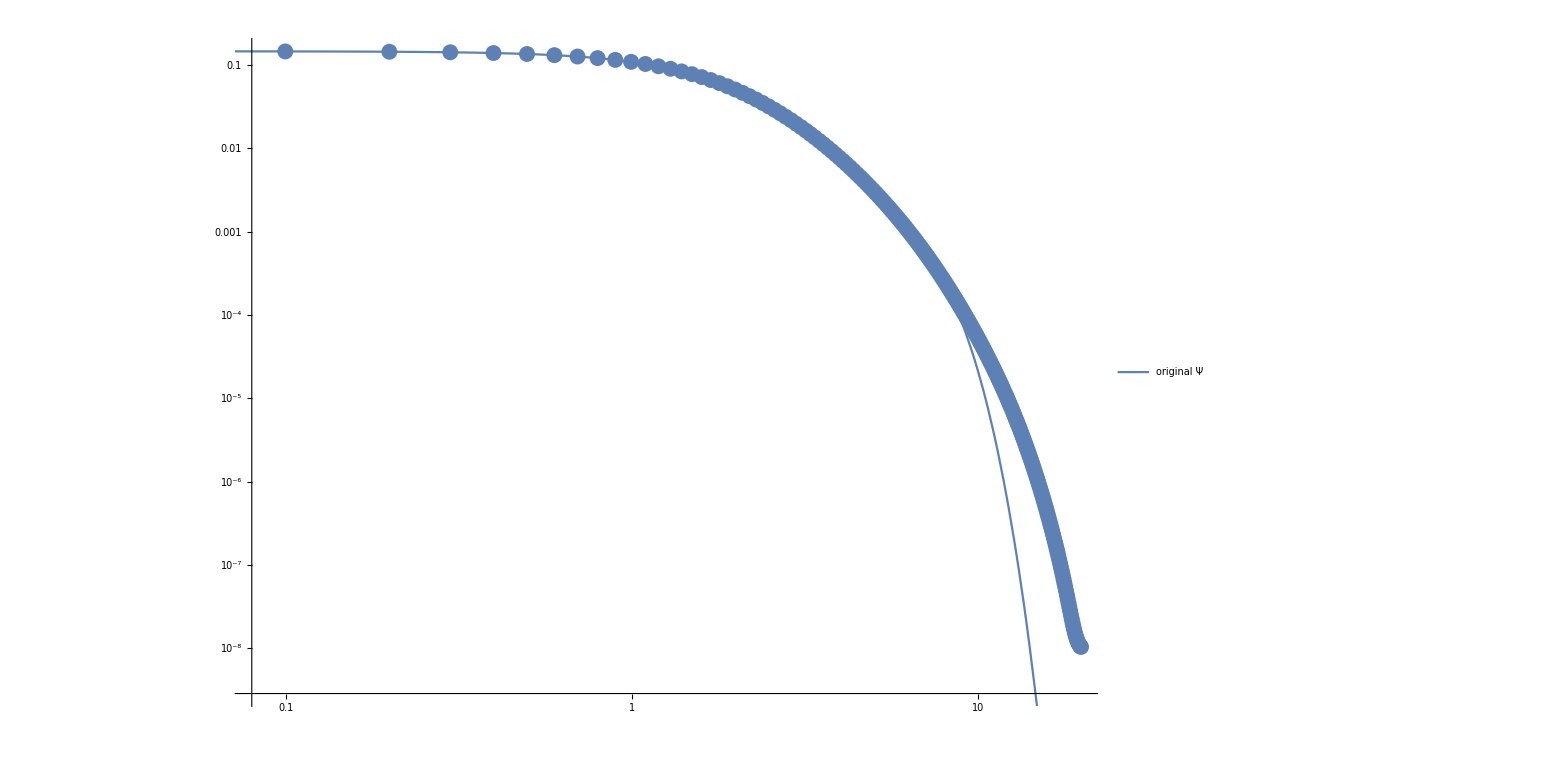

λ=2.  , core={{-0.537416,0.127388},{0.145614,0.708593},{0.114445,0.0971138},{0.49039,0.140968}}

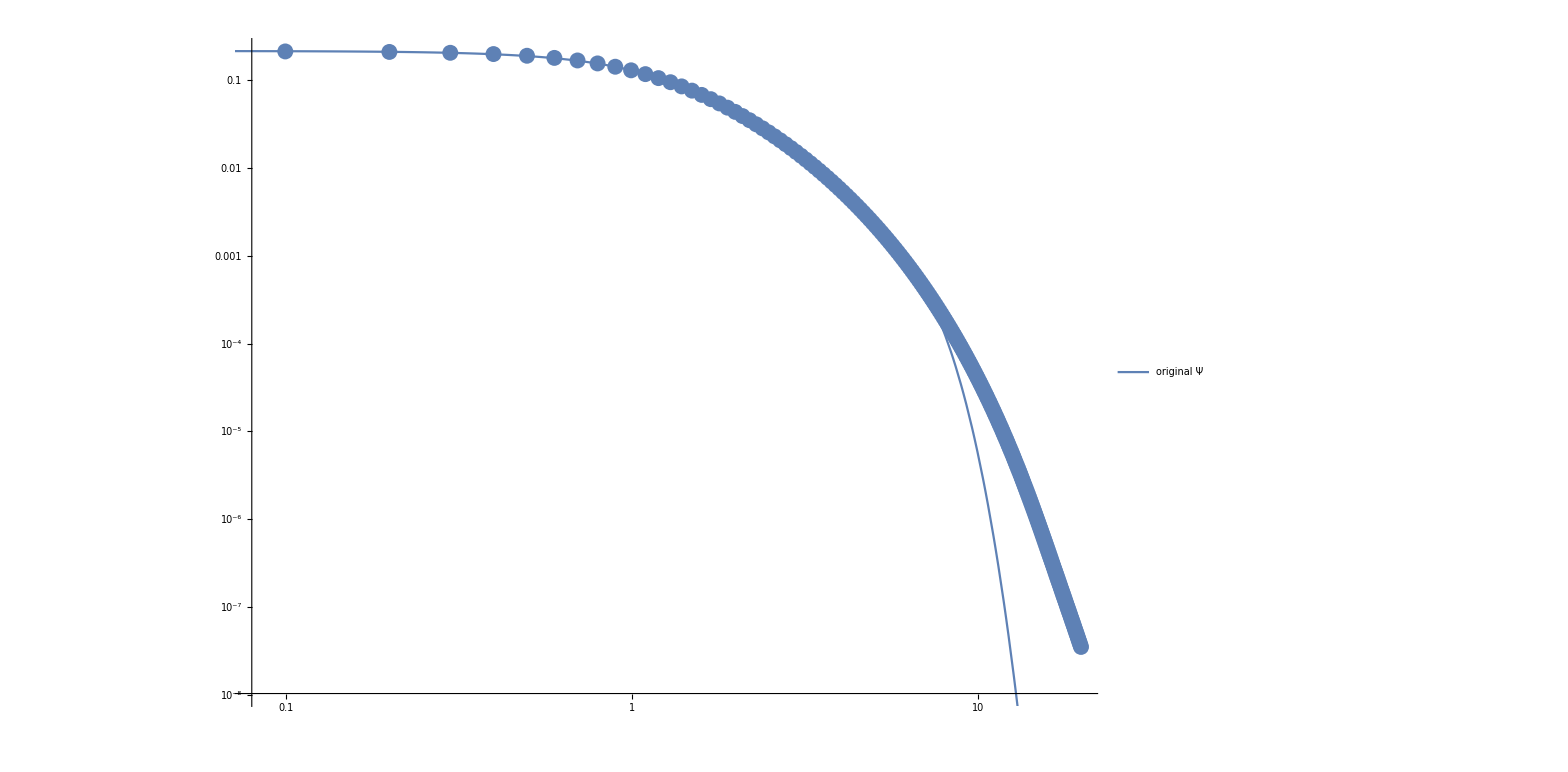

λ=3.  , core={{-0.991101,0.14294},{0.238553,0.115201},{0.175435,0.93149},{0.829989,0.156442}}

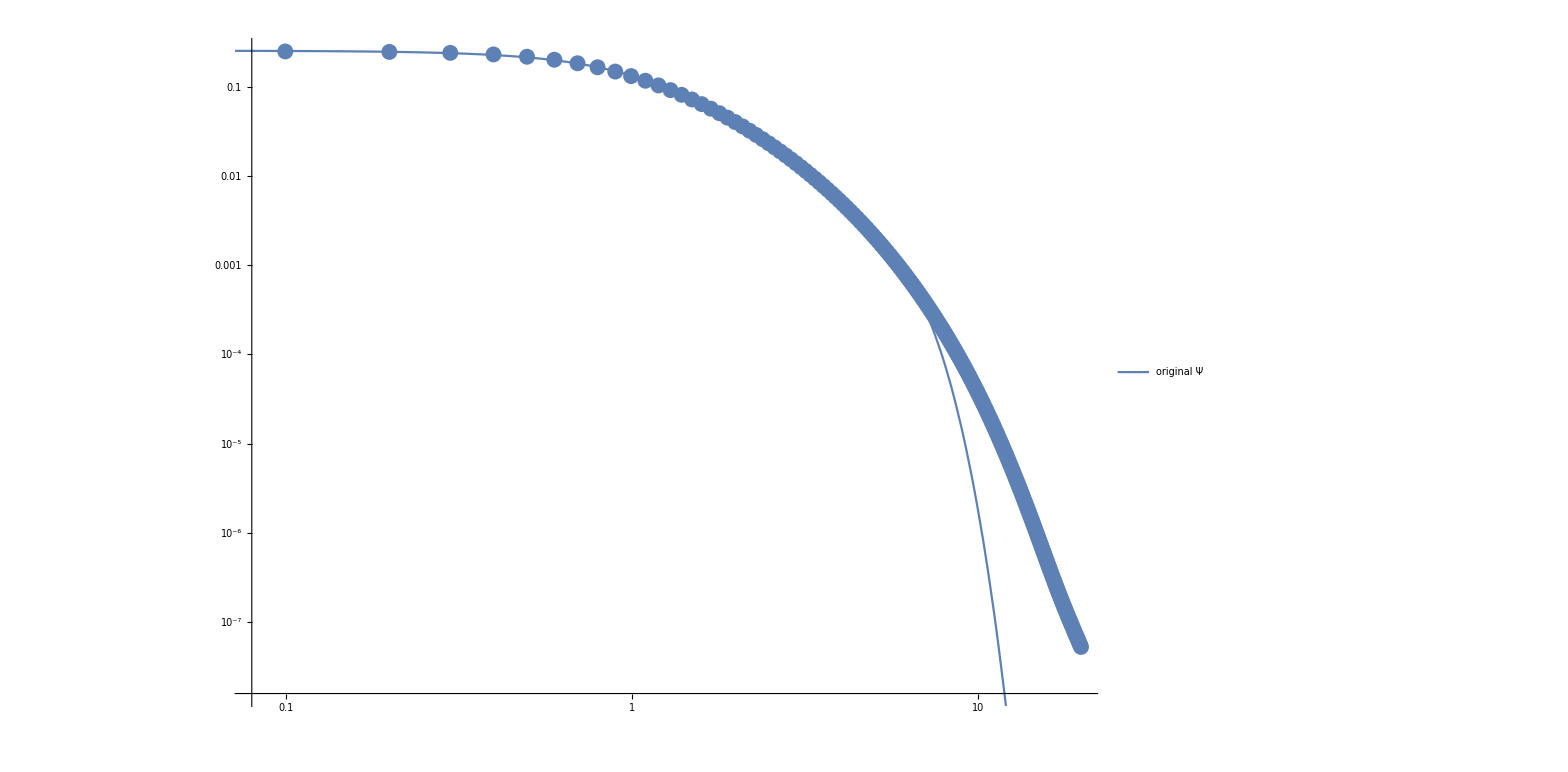

λ=4.  , core={{-1.35441,0.155064},{0.350175,0.127759},{1.08939,0.169127},{0.194014,1.10034}}

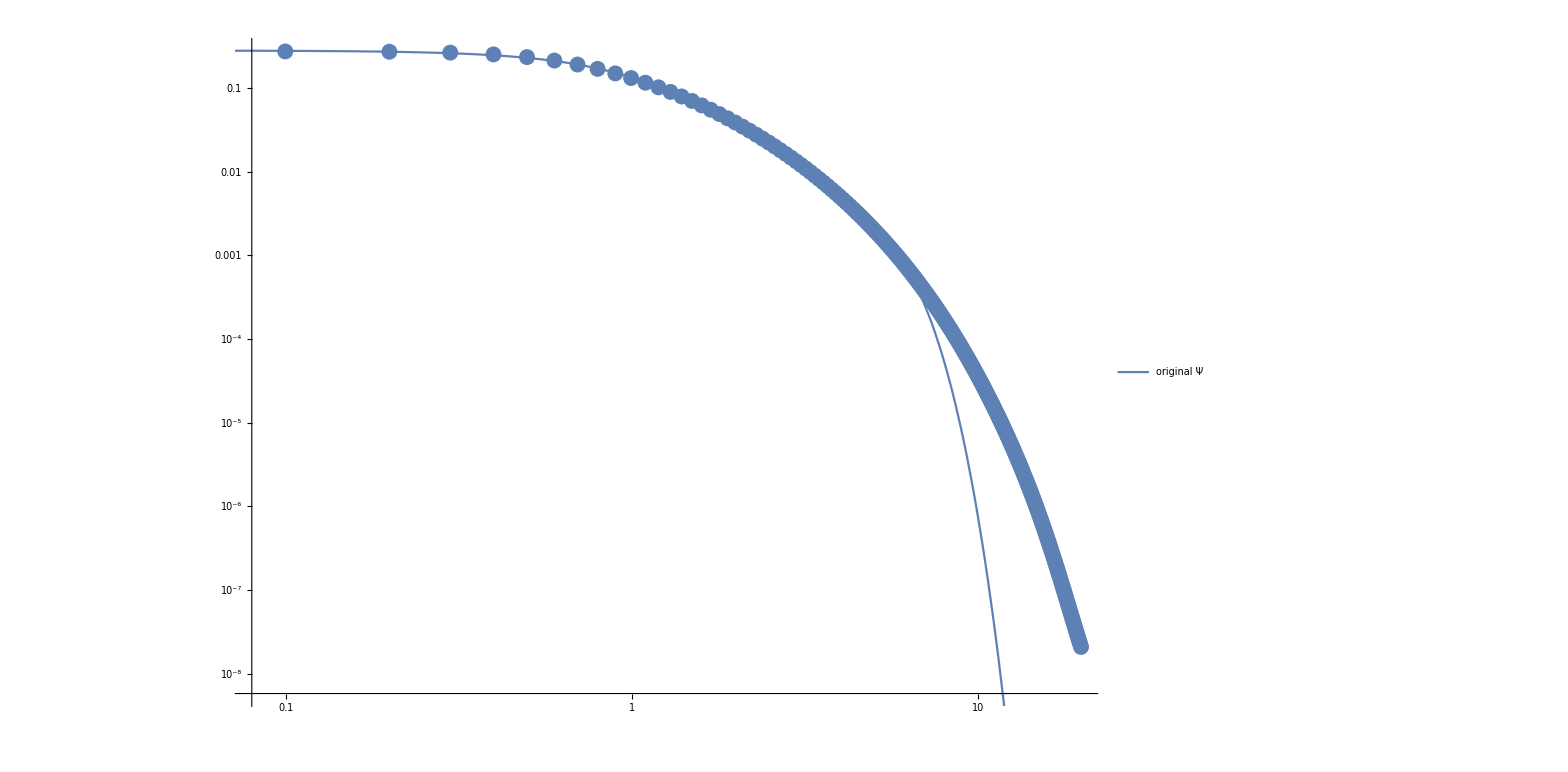

λ=6.  , core={{1.99641,0.706289},{-0.566502,0.706289},{-0.566502,0.706289},{-0.566502,0.706289}}

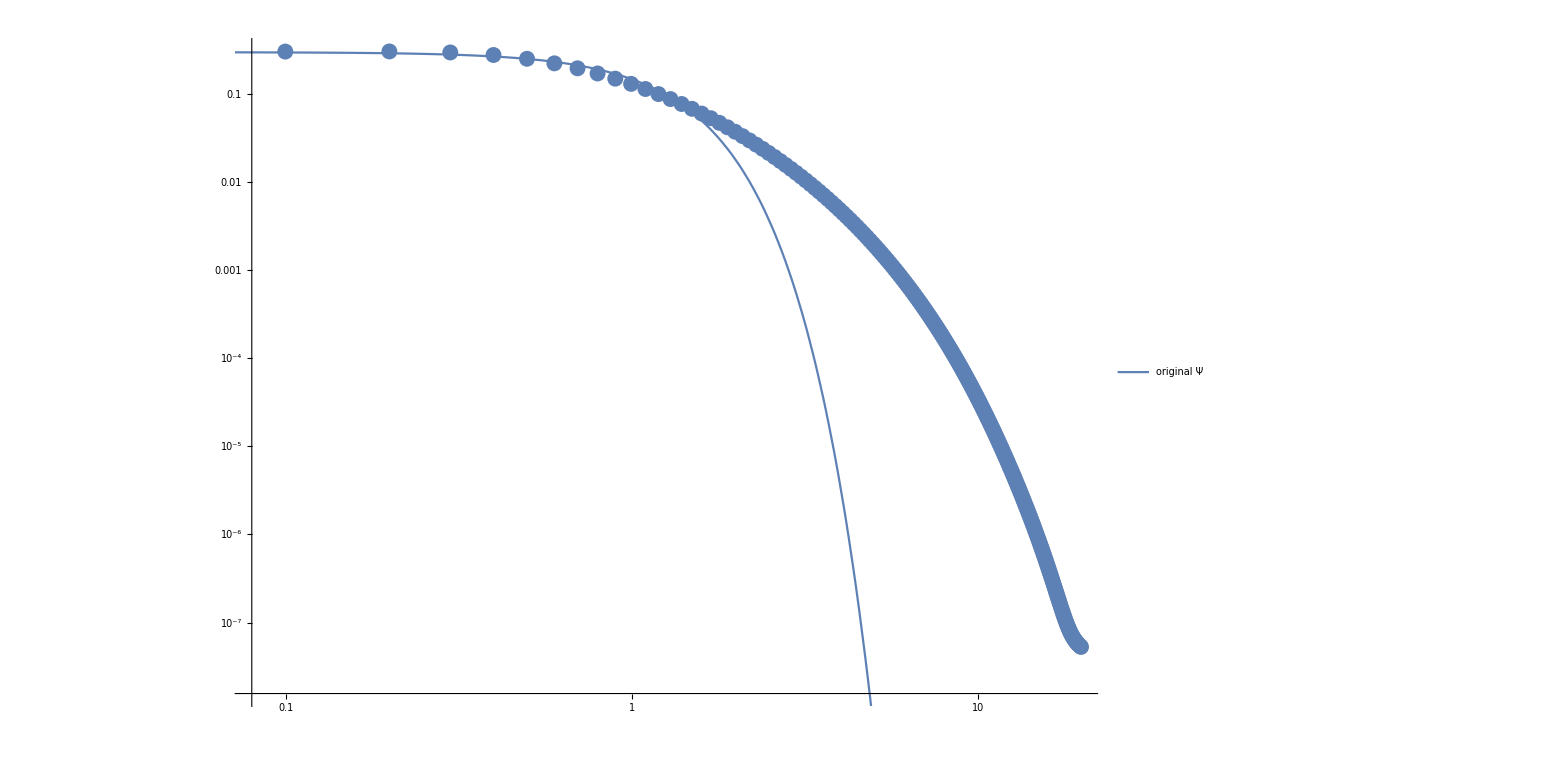

λ=8.  , core={{1.0237,0.76783},{-0.236569,0.76783},{-0.236569,0.76783},{-0.236569,0.76783}}

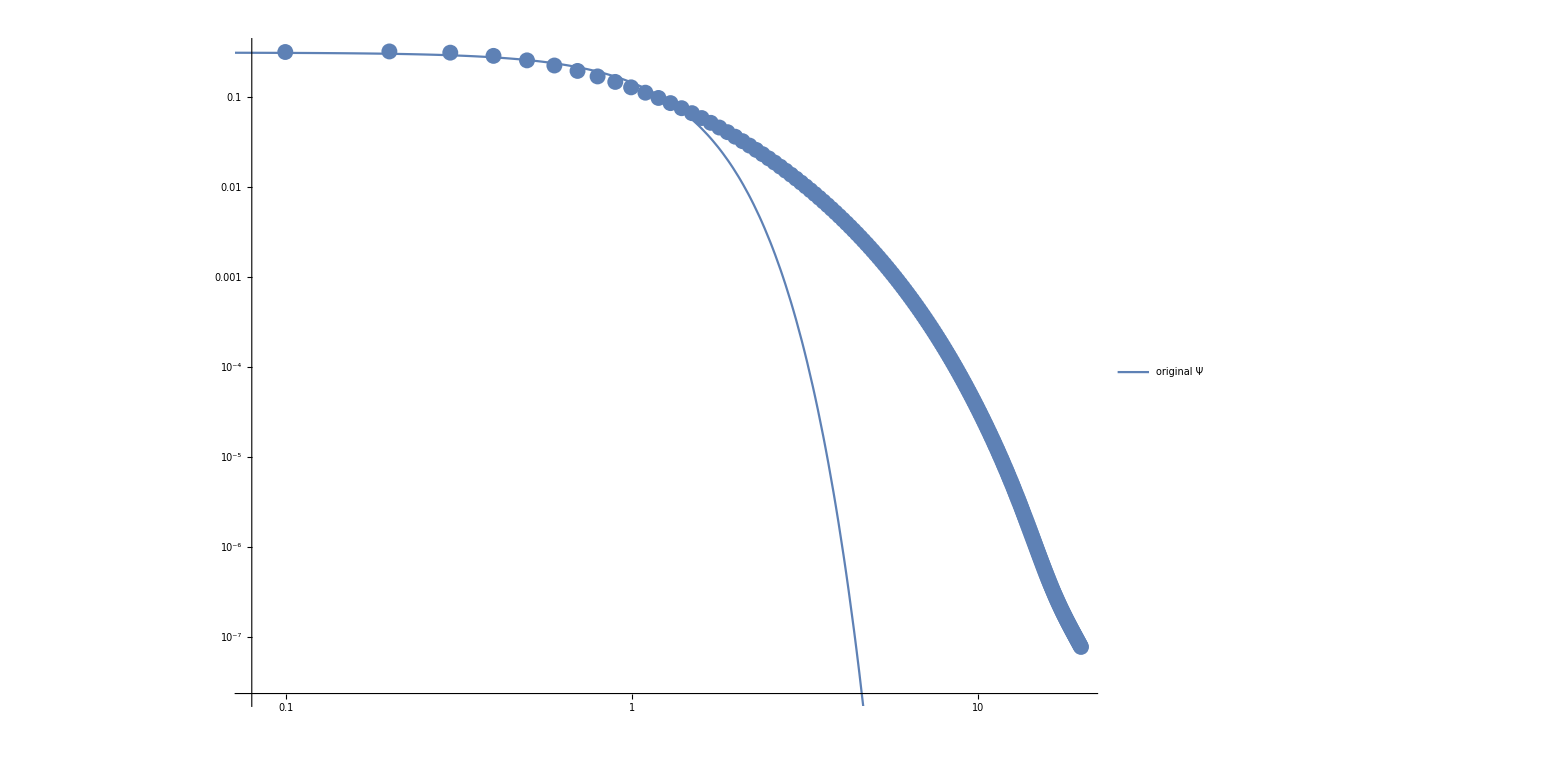

λ=10.  , core={{0.236034,1.61883},{0.0142675,0.079202},{0.0499707,0.334293},{0.0463896,0.334293}}

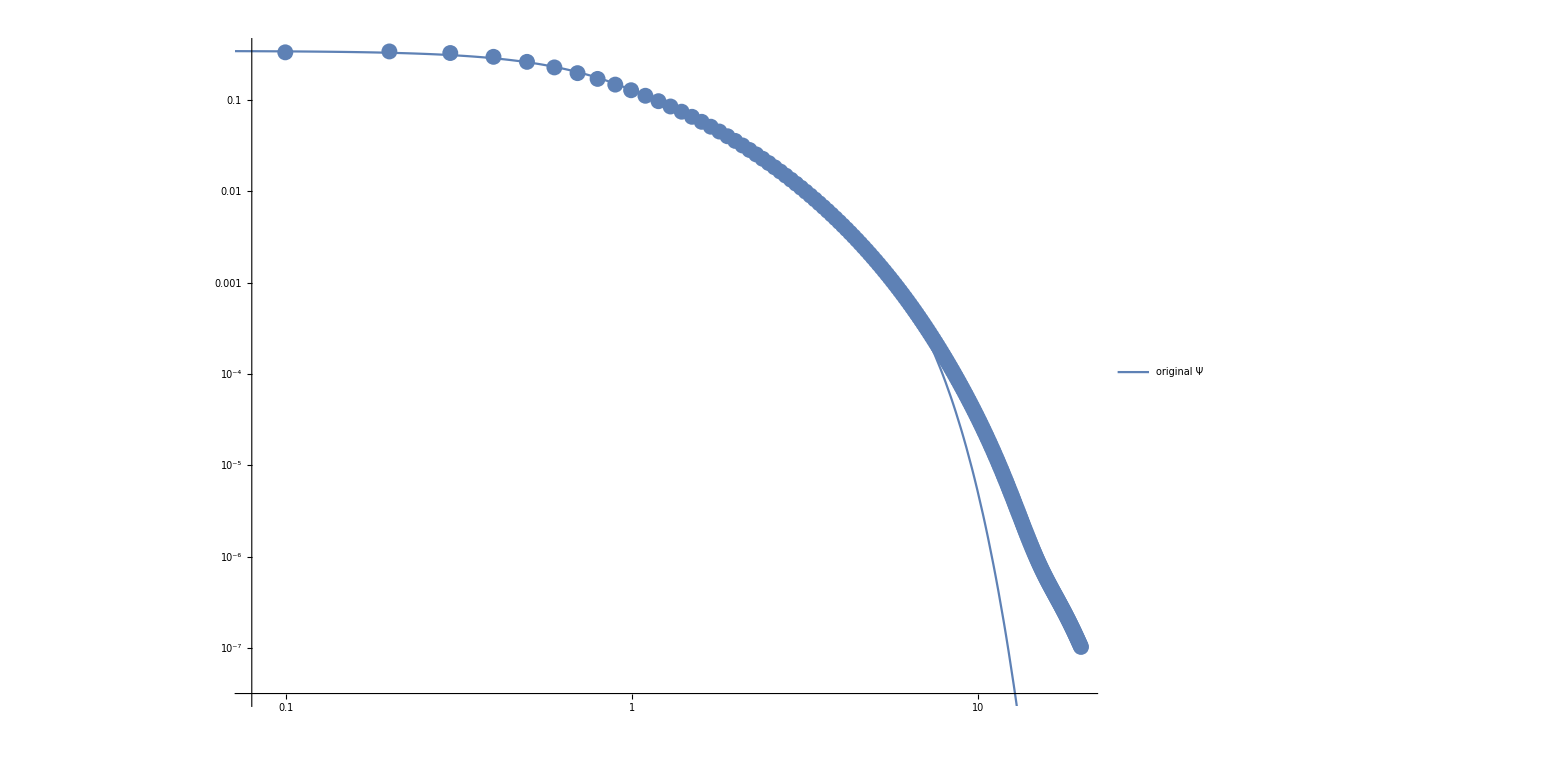

```mathematica
nk=4;

rmip=0.0;
rmap=21;

wfCores={};
wfs={};
w1=1+0 Floor[Length[Mϕ[[1]]]/8];
cmin=0;cmax=10^2;
amin=0.00001;amax=1.2;
w2=-1;
Do[
core={}; Do[core=AppendTo[core,ToExpression@Map[StringJoin[#,ToString[k]]&,{"C","Α"}]],{k,1,nk}];
wf=Total[Flatten[Table[core⟦i⟧⟦1⟧ⅇ^(-core⟦i⟧⟦2⟧ r^2) ,{i,Length[core]}]]];
data=MϕNfit[[ll]][[w1;;w2]];
(* initial values for the fit parameters *)
inicond=Union[{#,RandomReal[{cmin,cmax}]}&/@Flatten[core][[;;;;2]],{#,RandomReal[{amin,amax}]}&/@Flatten[core][[2;;;;2]]];
(* constraints for the fit parameters *)
bcs=Flatten[Table[{amin<core⟦i⟧⟦2⟧<amax,cmin<core⟦i⟧⟦1⟧<cmax},{i,Length[core]}]];
(*AppendTo[wfCores,core/.FindFit[data,{wf,bcs},inicond,r]];*)
(*AppendTo[wfCores,core/.FindFit[data,{wf,bcs},Flatten[core],r]];*)
(*AppendTo[wfCores,core/.FindFit[data,wf,Flatten[core],r,Method->"LevenbergMarquardt"]];*)
AppendTo[wfCores,core/.FindFit[data,wf r^tailweight,Flatten[core],r,Method->"LevenbergMarquardt"]];
corefit=Transpose[{Flatten[core],Flatten[wfCores[[-1]]]}];
AppendTo[wfs,Total[Flatten[Table[wfCores[[-1]]⟦i⟧⟦1⟧ⅇ^(-wfCores[[-1]]⟦i⟧⟦2⟧ r^2) ,{i,Length[wfCores[[-1]]]}]]]];
Print["λ=",wflambdas[[ll]],"  , core=",wfCores[[-1]]];
Show[ListLogLogPlot[Mϕ[[ll]]],
LogLogPlot[wfs[[-1]],{r,rmip,rmap},PlotLegends->{"original Ψ"},PlotRange->Full(*,Epilog->Map[Point,Mϕ[[ll]]]*)(*,Plot[wfsC[[nwf]],{r,0,rmap},PlotStyle->{Blue,Dashed}]*),ImageSize->1250, AxesLabel->{"r [fm]","WaveFunction"}(*,
PlotLabel->"Λ = "<>ToString[wflambdas[[nwf]]]<>" fm^-1"<>"  ;  f_fit=∑_(n = 1)^N c_n·e^(-SubscriptBox[α, n]·SuperscriptBox[ρ, 2]) with N="<>ToString[nk]<>"    Case: "<>ToString[sy]]*)],ImageSize->1250]//Print
,{ll,Range[Length[wflambdas]]}];
```

## The real pudding

```mathematica
rGrid={9.2}; (* Subdivide[6.5,12.1,1] *)
rr=rGrid[[1]];
EREs={};

nGrid=90;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.005;
k0FMax=0.02;
Divisions=5;

(*---------------------*)
ErangeMeV=N[findLogDivisions[{k0FMin^2/mh2,k0FMax^2/mh2},Divisions]];
Erange1onfm=Sqrt[mh2 ErangeMeV];
Do[
Do[
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==wflambdas[[nwf]]&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;
C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
mycore=wfCores[[nwf]];
Print[nn," ",nwf," ",λ," ",C0," ",mycore];
ERE=GetERE[mycore];
AppendTo[EREs,ERE];
Print["λ = Λ^2/4 = ",NumberForm[λ,nf](*,"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]*)," ; R_max = ",NumberForm[rr,nf],":   a0 = ", ERE⟦1⟧,"     r0 = ", ERE⟦2⟧,"     a1 = ", ERE⟦3⟧,"     r1 = ", ERE⟦4⟧]
,{nwf,{4}(*Range[Min[7,Length[wflambdas]]]*)}];
,{rr,rGrid}];
```

7 4 4. -505.15 {{0.127447,0.550093},{0.000542951,0.0293588},{0.00760561,0.0696422},{0.0377457,0.178618}}

λ = Λ^2/4 = 4.0000 ; R_max = 9.2000:   a0 = 0.633843     r0 = -3.54842     a1 = -0.0689165     r1 = 16.7098

Transpose::nmtx: The first two levels of {0.00001,-0.00308923} cannot be transposed.

Transpose::nmtx: The first two levels of {0.0001,-0.00976901} cannot be transposed.

Transpose::nmtx: The first two levels of {0.001,-0.0308923} cannot be transposed.

Transpose::nmtx: The first two levels of {0.01,-0.0976894} cannot be transposed.

Transpose::nmtx: The first two levels of {0.1,-0.308902} cannot be transposed.

Transpose::nmtx: The first two levels of {0.00001,6.21443×10^-9} cannot be transposed.

Transpose::nmtx: The first two levels of {0.0001,1.9651×10^-7} cannot be transposed.

Transpose::nmtx: The first two levels of {0.001,6.21181×10^-6} cannot be transposed.

Transpose::nmtx: The first two levels of {0.01,0.000195684} cannot be transposed.

Transpose::nmtx: The first two levels of {0.1,0.00596182} cannot be transposed.

S Pole Poitions in momentum: {-0.285684+0.304756 ⅈ,0.+0.376221 ⅈ,0.-0.985733 ⅈ,0.285684+0.304756 ⅈ}

S Pole Poitions in energy:   {-0.311339-4.81417 ⅈ,-3.91326+0. ⅈ,-26.8641+0. ⅈ,-0.311339+4.81417 ⅈ}

P Pole Poitions in momentum: {-0.405145-0.42077 ⅈ,0.+0.226107 ⅈ,0.-0.511195 ⅈ,0.405145-0.42077 ⅈ}

P Pole Poitions in energy:   {-0.356784+9.42625 ⅈ,-1.41345+0. ⅈ,-7.22481+0. ⅈ,-0.356784-9.42625 ⅈ}

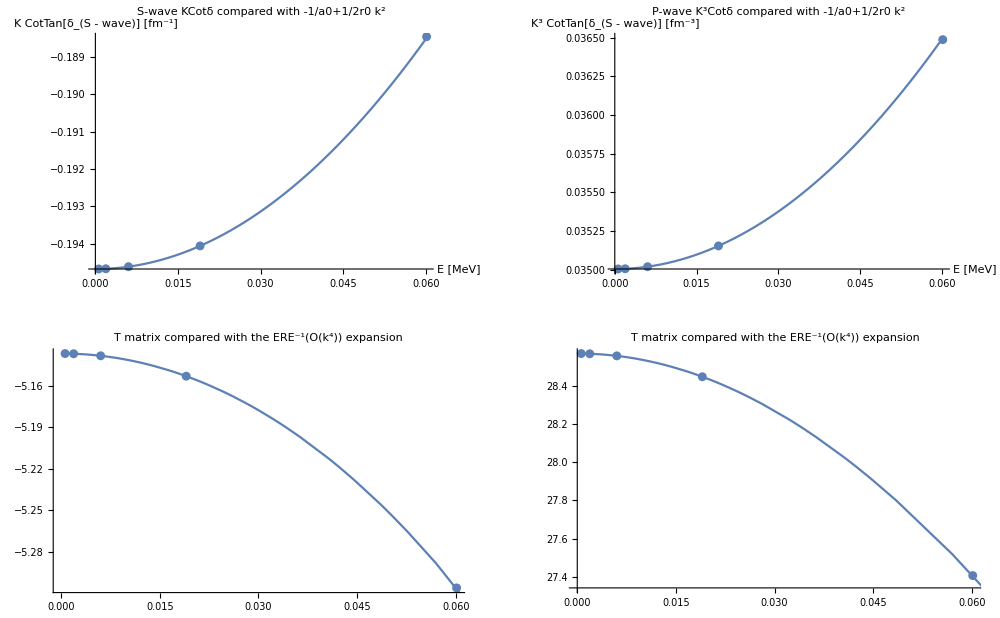

```mathematica
PlotERE
```

```mathematica
er=Table[EREs[[1+n Length[wflambdas];;(n+1) Length[wflambdas]]],{n,0,Length[rGrid]-1}];
model=a+b/x+c/x^2;
l0=2;
a0s=Transpose[{wflambdas,er[[#]][[All,1]]}]&/@Range[Length[rGrid]];
fita0=model/.FindFit[a0s[[-1]][[l0;;]],model,{a,b,c},x];
r0s=Transpose[{wflambdas,er[[#]][[All,2]]}]&/@Range[Length[rGrid]];
fitr0=model/.FindFit[r0s[[-1]][[l0;;]],model,{a,b,c},x];
a1s=Transpose[{wflambdas,er[[#]][[All,3]]}]&/@Range[Length[rGrid]];
fita1=model/.FindFit[a1s[[-1]][[l0;;]],model,{a,b,c},x];
r1s=Transpose[{wflambdas,er[[#]][[All,4]]}]&/@Range[Length[rGrid]];
fitr1=model/.FindFit[r1s[[-1]][[l0;;]],model,{a,b,c},x];
legs="R_max="<>ToString[#]&/@rGrid;
GraphicsGrid[{{
Show[ListPlot[a0s,PlotLegends->Placed[legs,Above],AxesLabel->{MaTeX["\\lambda [\\textrm{fm}^{-2}]",Magnification->2],MaTeX["a_S [\\textrm{fm}]",Magnification->2]},ImageSize->Large,PlotLabel->"lim _(λ → ∞) a_S = "<>ToString[Limit[fita0,x->Infinity]]<>" fm"],Plot[fita0,{x,0,10},ImageSize->Large]],
Show[ListPlot[r0s,AxesLabel->{MaTeX["\\lambda [\\textrm{fm}^{-2}]",Magnification->2],MaTeX["r_S [\\textrm{fm}]",Magnification->2]},ImageSize->Large,PlotLabel->"lim _(λ → ∞) r_S = "<>ToString[Limit[fitr0,x->Infinity]]<>" fm"],Plot[fitr0,{x,0,10},ImageSize->Large]]
},{
Show[ListPlot[a1s,PlotLegends->Placed[legs,Above],AxesLabel->{MaTeX["\\lambda [\\textrm{fm}^{-2}]",Magnification->2],MaTeX["a_P [\\textrm{fm}^3]",Magnification->2]},ImageSize->Large,PlotLabel->"lim _(λ → ∞) a_P = "<>ToString[Limit[fita1,x->Infinity]]<>" fm^3"],Plot[fita1,{x,0,10},ImageSize->Large]],
Show[ListPlot[r1s,AxesLabel->{MaTeX["\\lambda [\\textrm{fm}^{-2}]",Magnification->2],MaTeX["r_P [\\textrm{fm}^{-1}]",Magnification->2]},ImageSize->Large,PlotLabel->"lim _(λ → ∞) r_P = "<>ToString[Limit[fitr1,x->Infinity]]<>" fm^-1"],Plot[fitr1,{x,0,10},ImageSize->Large]]
}}]
```

-Graphics-

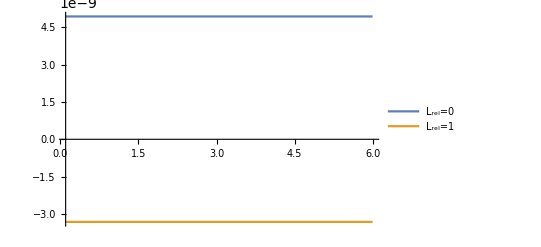

-Graphics3D-

25.

-2929.17

92495

```mathematica
nwf=7;
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==wflambdas[[nwf]]&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;
C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
mycore=wfCoresC[[nwf]];
rprime=2.1;sca=1.;rMax=6;
Plot[{WnolocTF[rMax,rprime,ErangeMeV[[2]],λ,C0,D0,mycore[[1]][[2]],mycore[[2]][[2]],0,mh2],WnolocTF[rMax,rprime,ErangeMeV[[2]],λ,sca C0,sca D0,mycore[[1]][[2]],mycore[[2]][[2]],1,mh2]},{rr,0.1,rMax},PlotRange->Full,PlotLegends->{"L_rel=0","L_rel=1"}]

Plot3D[{(*WnolocTF[rr,rp,ErangeMeV[[-1]],λ,sca C0,sca D0,mycore[[1]][[2]],mycore[[2]][[2]],1,mh2],*)WnolocTF[rr,rp,ErangeMeV[[-1]],λ,C0,D0,mycore[[1]][[2]],mycore[[2]][[2]],1,mh2]},{rr,0.1,rMax},{rp,0.1,rMax},PlotRange->Full,PlotLegends->{"E="<>ToString[ErangeMeV[[1]]],"E="<>ToString[ErangeMeV[[2]]]},PlotStyle->{Directive[Opacity[0.2],Orange, Specularity[White,50]],None},ImageSize->750]
λ
C0
D0
```